{0,0}

{{5/12,-1/(2 √3)-(√3)/4},{7/12,-(√3)/4},{5/12,1/(2 √3)-(√3)/4},{1/12,1/(2 √3)-(√3)/4},{-1/12,-(√3)/4},{1/12,-1/(2 √3)-(√3)/4},{2/3,-1/(2 √3)},{5/6,0},{2/3,1/(2 √3)},{1/3,1/(2 √3)},{1/6,0},{1/3,-1/(2 √3)},{5/12,-1/(2 √3)+(√3)/4},{7/12,(√3)/4},{5/12,1/(2 √3)+(√3)/4},{1/12,1/(2 √3)+(√3)/4},{-1/12,(√3)/4},{1/12,-1/(2 √3)+(√3)/4},{{-1/12,-1/(2 √3)+(√3)/4},{1/12,(√3)/4},{-1/12,1/(2 √3)+(√3)/4},{-5/12,1/(2 √3)+(√3)/4},{-7/12,(√3)/4},{-5/12,-1/(2 √3)+(√3)/4}},{{-1/3,-1/(2 √3)},{-1/6,0},{-1/3,1/(2 √3)},{-2/3,1/(2 √3)},{-5/6,0},{-2/3,-1/(2 √3)}},{{-1/12,-1/(2 √3)-(√3)/4},{1/12,-(√3)/4},{-1/12,1/(2 √3)-(√3)/4},{-5/12,1/(2 √3)-(√3)/4},{-7/12,-(√3)/4},{-5/12,-1/(2 √3)-(√3)/4}},{{5/12,-1/(2 √3)-(√3)/4},{7/12,-(√3)/4},{5/12,1/(2 √3)-(√3)/4},{1/12,1/(2 √3)-(√3)/4},{-1/12,-(√3)/4},{1/12,-1/(2 √3)-(√3)/4}},{{2/3,-1/(2 √3)},{5/6,0},{2/3,1/(2 √3)},{1/3,1/(2 √3)},{1/6,0},{1/3,-1/(2 √3)}},{{5/12,-1/(2 √3)+(√3)/4},{7/12,(√3)/4},{5/12,1/(2 √3)+(√3)/4},{1/12,1/(2 √3)+(√3)/4},{-1/12,(√3)/4},{1/12,-1/(2 √3)+(√3)/4}},{{-1/12,-1/(2 √3)+(√3)/4},{1/12,(√3)/4},{-1/12,1/(2 √3)+(√3)/4},{-5/12,1/(2 √3)+(√3)/4},{-7/12,(√3)/4},{-5/12,-1/(2 √3)+(√3)/4}},{{-1/3,-1/(2 √3)},{-1/6,0},{-1/3,1/(2 √3)},{-2/3,1/(2 √3)},{-5/6,0},{-2/3,-1/(2 √3)}},{{-1/12,-1/(2 √3)-(√3)/4},{1/12,-(√3)/4},{-1/12,1/(2 √3)-(√3)/4},{-5/12,1/(2 √3)-(√3)/4},{-7/12,-(√3)/4},{-5/12,-1/(2 √3)-(√3)/4}}}

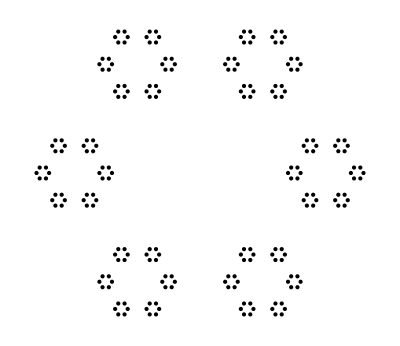

{{0,0},{1,1},{1,1}}

Set::write: Tag List in {0,0}[{x_,0}] is Protected.

SetDelayed::write: Tag List in {0,0}[{x_,n_}] is Protected.

$Failed

{0,0}[{{0,0},2}]

```mathematica
createCirclyCoords[{point_, scale_}] := Table[point + x*scale,{x,CirclePoints[6]}]

(*FlattenAt[
Table[createCirclyCoords[{y,.125}], {y, 
FlattenAt[
Table[createCirclyCoords[{x, .25}], {x, CirclePoints[6]}],
Table[{a},{a, 1, 6, 1}]
]
}],
Table[{b},{b,1,36,1}]
]*)

w[1] = {0,0}
w[n_] := 
w[n] = 
FlattenAt[
Table[createCirclyCoords[{x, 1/n}], {x, w[n-1]}],
Table[{a},{a, 1, n, 1}]
]

w[3]

(*Graphics[Point[g[1]]]*)

Graphics[
Point[
FlattenAt[
Table[createCirclyCoords[{y,.05}], {y, 
FlattenAt[
Table[createCirclyCoords[{x, .25}], {x, CirclePoints[6]}],
Table[{a},{a, 1, 6, 1}]
]
}],
Table[{b},{b,1,36,1}]
]
]
]

f[{x_, 0}]=x;
f[{x_, n_}]:=f[{Append[x, {1,1}], n-1}]
f[{{{0,0}},2}]

d[{x_, 0}]=x;
d[{x_, n_}]:=
d[{
Append[createCirclyCoords[{x, .25}], x], 
n-1}
]

b = d[{{0,0},2}]
```